## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
data=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/6sem/6111/tables/data.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data//TableForm
```

№ | U, mV | Rп | Rм | T | 100*Sigma п | 10^4*Sigma м | 100/T | ln s | 
1. | -0.08 | 0.7703 | 0.091 | 26. | 0.3 | 6.69 | 3.34448 | -5.8 | 0.
2. | 0.12 | 0.604 | 0.0922 | 31. | 0.39 | 6.6 | 3.28947 | -5.56 | 0.24
3. | 0.32 | 0.4775 | 0.0937 | 36. | 0.49 | 6.49 | 3.23625 | -5.32 | 0.48
4. | 0.52 | 0.3805 | 0.0952 | 41. | 0.61 | 6.39 | 3.18471 | -5.09 | 0.71
5. | 0.72 | 0.307 | 0.0969 | 46. | 0.76 | 6.28 | 3.1348 | -4.88 | 0.92
6. | 0.92 | 0.2535 | 0.0984 | 51. | 0.92 | 6.18 | 3.08642 | -4.69 | 1.11
7. | 1.12 | 0.2095 | 0.1 | 56. | 1.11 | 6.08 | 3.03951 | -4.5 | 1.3
8. | 1.32 | 0.1736 | 0.1015 | 61. | 1.34 | 5.99 | 2.99401 | -4.31 | 1.49
9. | 1.52 | 0.1456 | 0.1031 | 66. | 1.6 | 5.9 | 2.94985 | -4.13 | 1.67
10. | 1.72 | 0.1215 | 0.1047 | 71. | 1.92 | 5.81 | 2.90698 | -3.95 | 1.85
11. | 1.92 | 0.1038 | 0.1063 | 76. | 2.25 | 5.72 | 2.86533 | -3.8 | 2.
12. | 2.12 | 0.0882 | 0.1078 | 81. | 2.64 | 5.64 | 2.82486 | -3.63 | 2.17
13. | 2.32 | 0.0757 | 0.1094 | 86. | 3.08 | 5.56 | 2.78552 | -3.48 | 2.32
14. | 2.52 | 0.0651 | 0.111 | 91. | 3.58 | 5.48 | 2.74725 | -3.33 | 2.47
15. | 2.72 | 0.0565 | 0.1125 | 96. | 4.13 | 5.41 | 2.71003 | -3.19 | 2.61
16. | 2.92 | 0.0501 | 0.114 | 101. | 4.65 | 5.34 | 2.6738 | -3.07 | 2.73

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[7.13007-0.0182294 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 7.13007 | 0.0202118 | 352.768 | 4.77367×10^-29
x | -0.0182294 | 0.000299196 | -60.9281 | 2.21744×10^-18

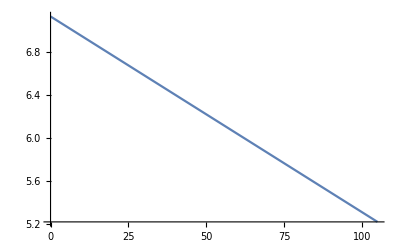

```mathematica
forFitCu=data⟦2;;,{5,7}⟧;
fitCu=LinearModelFit[forFitCu,{1,x},x]
fitCu@"ParameterTable"
Plot[fitCu["Function"]@x, {x, 0, 105}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

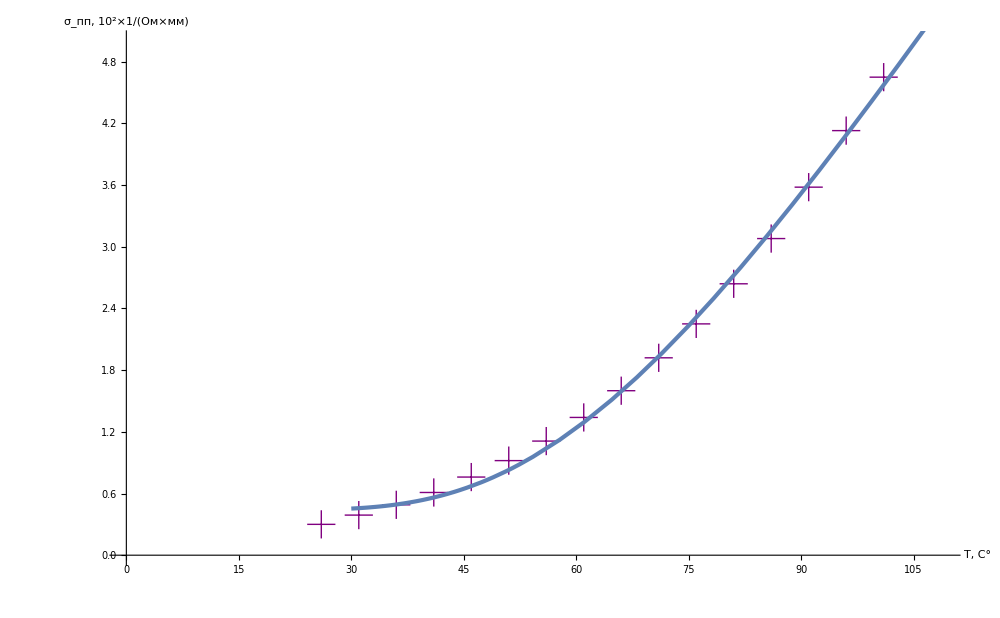

```mathematica
Show[ListPlot[data⟦2;;,{5,6}⟧,
GridLines->{grids@2,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"T, C°","σ_(:043f:043f), 10^2×1/(:041e:043c×:043c:043c)"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
PlotMarkers->{"+", 29},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,109},{0,5}}], 
Plot[fitPP["Function"]@x,{x,30,200}, PlotStyle->Thickness@0.003]]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

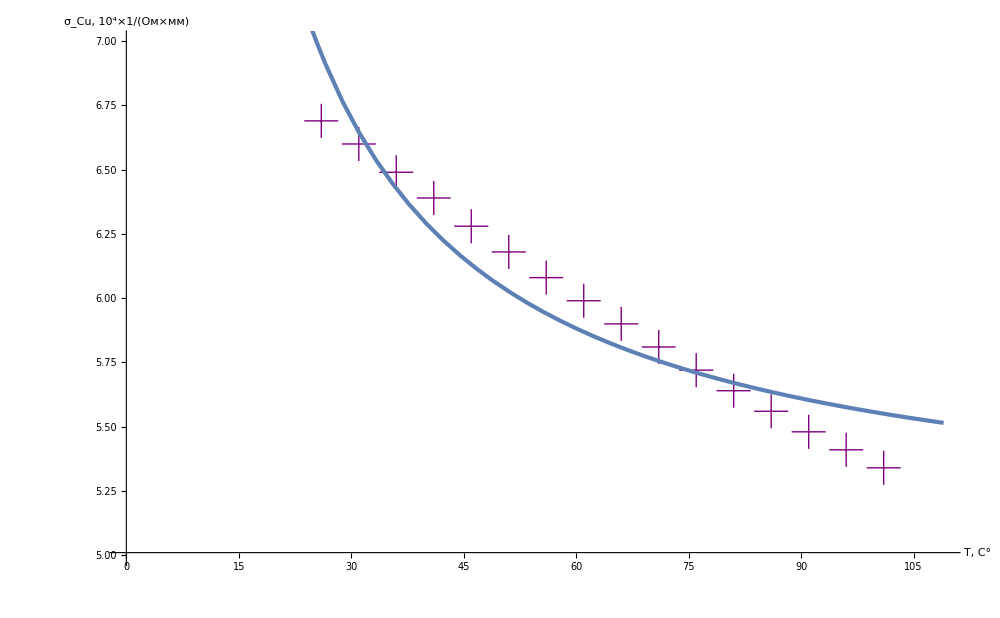

```mathematica
Show[ListPlot[data⟦2;;,{5,7}⟧,
GridLines->{grids@2,grids@0.2},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"T, C°","σ_Cu, 10^4×1/(:041e:043c×:043c:043c)"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
PlotMarkers->{"+", 35},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{0,109},{5,7}}], 
Plot[fitEe["Function"]@x,{x,0,109}, PlotStyle->Thickness@0.003]]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

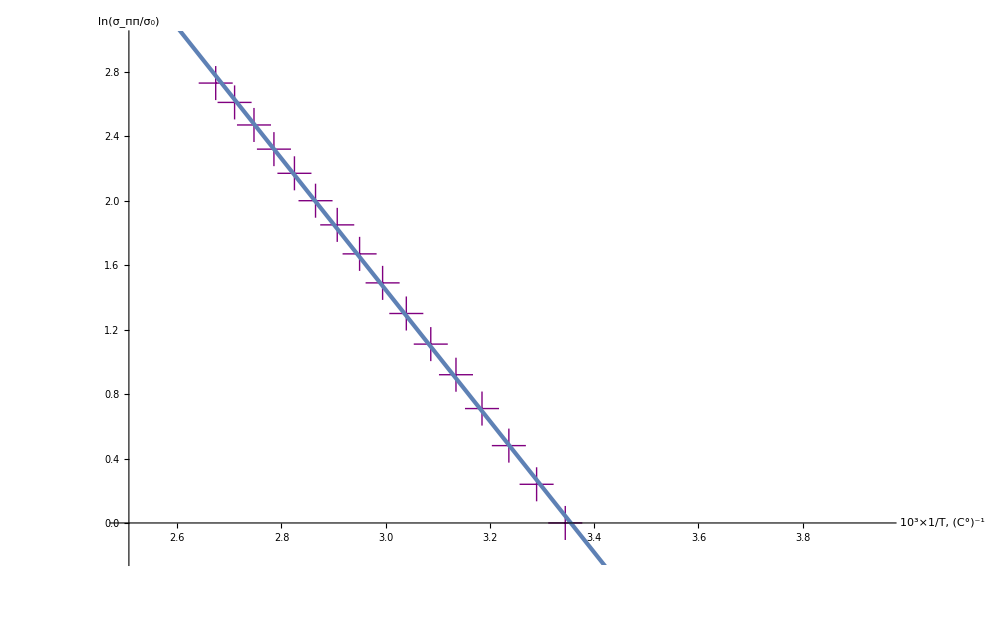

```mathematica
Show[ListPlot[data⟦2;;,{8,10}⟧,
GridLines->{grids@0.1,grids@0.2},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"10^3×1/T, (C°)^-1","ln((σ_(:043f:043f))/σ_0)"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotStyle->{Thickness@0.003 ,Purple},
PlotMarkers->{"+", 35},
(*Ticks->{myTicksX, myTicksY}, *)
PlotRange->{{2.5,3.95},{-0.2,2.99}}], 
Plot[fit["Function"]@x,{x,0,109}, PlotStyle->Thickness@0.003]]
```

### Импорт табличных данных

```mathematica
dataF=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/6sem/6111/tables/df.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataF//TableForm
```

9. | 1.52 | 0.1456 | 0.1031 | 66. | 1.6 | 5.90054 | 0.0151515 | -4.13 | 1.67
10. | 1.72 | 0.1215 | 0.1047 | 71. | 1.92 | 5.81037 | 0.0140845 | -3.95 | 1.85
11. | 1.92 | 0.1038 | 0.1063 | 76. | 2.25 | 5.72291 | 0.0131579 | -3.8 | 2.
12. | 2.12 | 0.0882 | 0.1078 | 81. | 2.64 | 5.64328 | 0.0123457 | -3.63 | 2.17
13. | 2.32 | 0.0757 | 0.1094 | 86. | 3.08 | 5.56074 | 0.0116279 | -3.48 | 2.32
14. | 2.52 | 0.0651 | 0.111 | 91. | 3.58 | 5.48059 | 0.010989 | -3.33 | 2.47
15. | 2.72 | 0.0565 | 0.1125 | 96. | 4.13 | 5.40751 | 0.0104167 | -3.19 | 2.61
16. | 2.92 | 0.0501 | 0.114 | 101. | 4.65 | 5.33636 | 0.00990099 | -3.07 | 2.73

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[13.6679-4.07374 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 13.6679 | 0.0853993 | 160.047 | 3.04101×10^-24
x | -4.07374 | 0.0285339 | -142.768 | 1.50392×10^-23

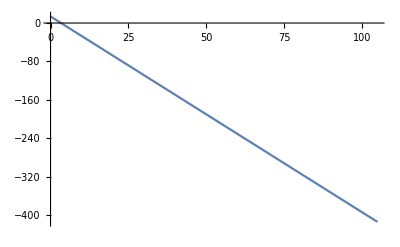

```mathematica
forFit=data⟦2;;,{8,10}⟧;
fit=LinearModelFit[forFit,{1,x},x]
fit@"ParameterTable"
Plot[fit["Function"]@x, {x, 0, 105}]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

\left(
\begin{array}{cccccccccc}
 \unicode{2116} & \text{U, mV} & \text{R$\unicode{043f}$} & \text{R$\unicode{043c}$} & \text{T} & \text{100*Sigma $\unicode{043f}$} & \text{10${}^{\wedge}$4*Sigma
   $\unicode{043c}$} & \text{100/T} & \text{ln s} & \text{} \\
 1 & -0.08 & 0.7703 & 0.091 & 26 & 0.3 & 6.69 & 3.85 & -5.8 & 0 \\
 2 & 0.12 & 0.604 & 0.0922 & 31 & 0.39 & 6.6 & 3.23 & -5.56 & 0.24 \\
 3 & 0.32 & 0.4775 & 0.0937 & 36 & 0.49 & 6.49 & 2.78 & -5.32 & 0.48 \\
 4 & 0.52 & 0.3805 & 0.0952 & 41 & 0.61 & 6.39 & 2.44 & -5.09 & 0.71 \\
 5 & 0.72 & 0.307 & 0.0969 & 46 & 0.76 & 6.28 & 2.17 & -4.88 & 0.92 \\
 6 & 0.92 & 0.2535 & 0.0984 & 51 & 0.92 & 6.18 & 1.96 & -4.69 & 1.11 \\
 7 & 1.12 & 0.2095 & 0.1 & 56 & 1.11 & 6.08 & 1.79 & -4.5 & 1.3 \\
 8 & 1.32 & 0.1736 & 0.1015 & 61 & 1.34 & 5.99 & 1.64 & -4.31 & 1.49 \\
 9 & 1.52 & 0.1456 & 0.1031 & 66 & 1.6 & 5.9 & 1.52 & -4.13 & 1.67 \\
 10 & 1.72 & 0.1215 & 0.1047 & 71 & 1.92 & 5.81 & 1.41 & -3.95 & 1.85 \\
 11 & 1.92 & 0.1038 & 0.1063 & 76 & 2.25 & 5.72 & 1.32 & -3.8 & 2 \\
 12 & 2.12 & 0.0882 & 0.1078 & 81 & 2.64 & 5.64 & 1.23 & -3.63 & 2.17 \\
 13 & 2.32 & 0.0757 & 0.1094 & 86 & 3.08 & 5.56 & 1.16 & -3.48 & 2.32 \\
 14 & 2.52 & 0.0651 & 0.111 & 91 & 3.58 & 5.48 & 1.1 & -3.33 & 2.47 \\
 15 & 2.72 & 0.0565 & 0.1125 & 96 & 4.13 & 5.41 & 1.04 & -3.19 & 2.61 \\
 16 & 2.92 & 0.0501 & 0.114 & 101 & 4.65 & 5.34 & 0.99 & -3.07 & 2.73 \\
\end{array}
\right)

```mathematica
{{"", "Estimate", "Standard Error"}, {1, 7.130004835048526, 0.018711547232453843}, {x, -0.018222896055882305, 0.00027698782034633754}}
```

{{,Estimate,Standard Error},{1,7.13,0.0187115},{x,-0.0182229,0.000276988}}

```mathematica
TeXForm[{{"","Estimate","Standard Error"},{1,7.130004835048526,0.018711547232453843},{x,-0.018222896055882305,0.00027698782034633754}}]
```

\left(
\begin{array}{ccc}
 \text{} & \text{Estimate} & \text{Standard Error} \\
 1 & 7.13 & 0.0187115 \\
 x & -0.0182229 & 0.000276988 \\
\end{array}
\right)

```mathematica
{{1, 4.831854723080561, 0.0736901982241068}, {x, -2.1410452869339487, 0.06207650673558916}}
```

{{1,4.83185,0.0736902},{x,-2.14105,0.0620765}}

```mathematica
TeXForm[{{1,4.831854723080561,0.0736901982241068},{x,-2.1410452869339487,0.06207650673558916}}]
```

\left(
\begin{array}{ccc}
 1 & 4.83185 & 0.0736902 \\
 x & -2.14105 & 0.0620765 \\
\end{array}
\right)

### Построение графика линейной функции + табличные данные без крестов

```mathematica
model =a*Exp[b/x]+c
```

c+a ⅇ^(b/x)

```mathematica
(*fit1=NonlinearModelFit[forFitN⟦All,{1,2}⟧,{model1,-5<g<5},{{a,5},{c,0.3},{d,2},{f, 4.4},{e,2},{g,0}},x]*)
fitPP=NonlinearModelFit[forFitPP,model,{a,b,c},x]
(*fitP=NonlinearModelFit[forFitN⟦All,{3,2}⟧,{modelm(*,-0.2<g<1,1<a<4.5,3<b<4.1,0<c<10, 0.19<d<5, 4<f<5,0<e<10, -5<g<5*)},{{a,4.5},{b,1000},{c,100},{d,3},{f, 4.4},{e,2},{g,-0.2}},x(*, MaxIterations->10000*)]*)
fitPP@"ParameterTable"
(*fitP@"ParameterTable"*)
(*Plot[fit["Function"]@x, {x, 0, 32}] *)
```

FittedModel[0.439592+45.9876 ⅇ^(-243.311/x)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 45.9876 | 4.07299 | 11.2909 | 4.32385×10^-8
b | -243.311 | 8.70467 | -27.9517 | 5.376×10^-13
c | 0.439592 | 0.0392213 | 11.208 | 4.71886×10^-8

```mathematica
print@x_:=(Print@x;x);
```

```mathematica
forFitECr=datad⟦2;;,-1⟧
```

{10.26,11.07,12.42,5.13,9.18}

```mathematica
χ=Total[(print@fitE["FitResiduals"]/print@forFitECr)^2]/(Length[forFitE]-2)
χ^2
```

{20.008,20.6005,-18.3834,-38.3806,16.1555}

{10.26,11.07,12.42,5.13,9.18}

22.8427

521.79

```mathematica
gip=FittedModel[x/(1+x/255)]
```

FittedModel[x/(1+x/255)]

```mathematica
forFitPP=data⟦2;;,{5,6}⟧
```

{{26.,0.3},{31.,0.39},{36.,0.49},{41.,0.61},{46.,0.76},{51.,0.92},{56.,1.11},{61.,1.34},{66.,1.6},{71.,1.92},{76.,2.25},{81.,2.64},{86.,3.08},{91.,3.58},{96.,4.13},{101.,4.65}}

```mathematica
TableForm[forFitPP]
```

26. | 0.3
31. | 0.39
36. | 0.49
41. | 0.61
46. | 0.76
51. | 0.92
56. | 1.11
61. | 1.34
66. | 1.6
71. | 1.92
76. | 2.25
81. | 2.64
86. | 3.08
91. | 3.58
96. | 4.13
101. | 4.65

```mathematica
{{1, 13.667863576584926, 0.08539929928155215}, {x, -4.0737390294445435, 0.02853392628108314}}
```

{{1,13.6679,0.0853993},{x,-4.07374,0.0285339}}

```mathematica
TeXForm[{{1,13.667863576584926,0.08539929928155215},{x,-4.0737390294445435,0.02853392628108314}}]
```

\left(
\begin{array}{ccc}
 1 & 13.6679 & 0.0853993 \\
 x & -4.07374 & 0.0285339 \\
\end{array}
\right)